```mathematica
S0=200;
X0={10^-4,10^-4};
y={10^-5,10^-5};
c={1,1};
d={1*10^-6,1*10^-6};
Ig={10,10};
a={10,10};
r={1,1,1};
max=0.01;
o={0,0,o3};
h=1;
M1=Table[i,{i,0.1,11,0.1}];
Ig0=Table[i,{i,0.1,10,0.1}];
Parasets1=Flatten[Table[{M1[[i]],Ig0[[j]]},{i,Length@M1},{j,Length@Ig0}],1];
O0={0,0.001,0.01,0.05,0.1};
Ig20={1,3,5,7,9};
Parasets2=Flatten[Table[{O0[[i]],Ig20[[j]]},{i,Length@O0},{j,Length@Ig20}],1]
Length@Parasets1
```

{{0,1},{0,3},{0,5},{0,7},{0,9},{0.001,1},{0.001,3},{0.001,5},{0.001,7},{0.001,9},{0.01,1},{0.01,3},{0.01,5},{0.01,7},{0.01,9},{0.05,1},{0.05,3},{0.05,5},{0.05,7},{0.05,9},{0.1,1},{0.1,3},{0.1,5},{0.1,7},{0.1,9}}

11000

```mathematica
para={y1,y2,c1,c2,d1,d2,Ig1,Ig2,a1,a2,rs,ri,rp,p,o1,o2,o3};
a1=a[[1]];
a2=a[[2]];
y1=y[[1]];
y2=y[[2]];
c1=c[[1]];
c2=c[[2]];
d1=d[[1]];
d2=d[[2]];
Ig1=Ig[[1]];
Ig2=Ig[[2]];
rs=r[[1]];
ri=r[[2]];
rp=r[[3]];
p=max;
o1=o[[1]];
o2=o[[2]];
o3=o[[3]];
```

```mathematica
Do[
o3=Parasets2[[k,1]];
Ig2=Parasets2[[k,2]];
List1={};
List2={};
Do[
m1=Parasets1[[i,1]];
Ig1=Parasets1[[i,2]];
c1=m1/((d2*Ig1*y1)/(c2*d1*Ig2*y2));
rs=r[[1]];
ri=r[[2]];
rp=r[[3]];
m1=(c1*d2*Ig1*y1)/(c2*d1*Ig2*y2);
m2=Ig1/rp;
var={sin1,sin2,sout,iin1,iin2,iout,pin1,pin2,pout,x1,x2};
t1=(Exp[-o1*sin1[t]])*(Exp[-o2*iin1[t]])*(Exp[-o3*pin1[t]]);
t2=(Exp[-o1*sin2[t]])*(Exp[-o2*iin2[t]])*(Exp[-o3*pin2[t]]);
eqn1={sin1'[t]==-a1+rs*(sout[t]-sin1[t]),
sin2'[t]==rs*(sout[t]-sin2[t]),
iin1'[t]==a1-ri*(iin1[t]-iout[t]),
iin2'[t]==-a2*iin2[t]+ri*(iout[t]-iin2[t]),
pin1'[t]==-Ig1*pin1[t]+rp*(pout[t]-pin1[t]),
pin2'[t]==a2*iin2[t]-Ig2*pin2[t]+rp*(pout[t]-pin2[t]),
sout'[t]==-x1[t]*rs*(sout[t]-sin1[t])-x2[t]*rs*(sout[t]-sin2[t]),
iout'[t]==x1[t]*ri*(iin1[t]-iout[t])-x2[t]*ri*(iout[t]-iin2[t]),
pout'[t]==x2[t]*rp*(pin2[t]-pout[t])-x1[t]*rp*(pout[t]-pin1[t]),
x1'[t]==(Ig1*c1*y1*t1*pin1[t]*x1[t]*(1-((x1[t]+x2[t])/p)))-d1*x1[t],
x2'[t]==(Ig2*c2*y2*t2*pin2[t]*x2[t]*(1-((x1[t]+x2[t])/p)))-d2*x2[t]
};
eqn2={sin1[0]==0,
sin2[0]==0,
sout[0]==S0,
iin1[0]==0,
iin2[0]==0,
iout[0]==0,
pin1[0]==0,
pin2[0]==0,
pout[0]==0,
x1[0]==X0[[1]],
x2[0]==X0[[2]]};
eqn=Join[eqn1,eqn2];
result=NDSolve[eqn,var,{t,0,100000000}];
ioutv=Flatten@Evaluate[iin1[90000000]/.result];
iin1v=Flatten@Evaluate[iin1[90000000]/.result];
iin2v=Flatten@Evaluate[iin2[90000000]/.result];
pin1v=Flatten@Evaluate[pin1[90000000]/.result];
pin2v=Flatten@Evaluate[pin2[90000000]/.result];
poutv=Flatten@Evaluate[pout[90000000]/.result];
x1b=Flatten@Evaluate[{x1[90000000]}/.result];
x2b=Flatten@Evaluate[{x2[90000000]}/.result];
biomass=x1b+x2b;
x1ratio=Flatten@Evaluate[{x1[90000000]/(x1[90000000]+x2[90000000])}/.result];
x2ratio=Flatten@Evaluate[{x2[90000000]/(x1[90000000]+x2[90000000])}/.result];
List1=Join[List1,{{First@iin1v,First@iin2v,First@pin1v,First@pin2v,First@ioutv,First@poutv,First@x1b,First@x2b,First@biomass,First@x1ratio,First@x2ratio}}];
List2=Join[List2,{{m1,m2,First@x2ratio,First@biomass}}];
If[Divisible[i,11000]==True,Print[k]];
,{i,1,Length@Parasets1}];
Export[FileNameJoin[{NotebookDirectory[],"list-exp","A="<>ToString@Parasets2[[k]]<>".xlsx"}],List1];
Export[FileNameJoin[{NotebookDirectory[],"list-exp","plot-A="<>ToString@Parasets2[[k]]<>".xlsx"}],List2];
,{k,1,1}];
```

1

```mathematica
O1={0,0.001,0.01,0.05,0.1};
Ig20={1,3,5,7,9};
Parasets3=Flatten[Table[{O0[[i]],Ig20[[j]]},{i,Length@O0},{j,Length@Ig20}],1];
Gridplot={};
Do[
data=Flatten[Import[FileNameJoin[{NotebookDirectory[],"list-exp","plot-A="<>ToString@Parasets3[[k]]<>".xlsx"}]],1];
Listplot=Table[{data[[m,1]]-1,data[[m,2]],If[data[[m,4]]<0.0001,-10,100*data[[m,3]]]},{m,Length@data}];
desplot=ListDensityPlot[Listplot,ColorFunction->"BlueGreenYellow",PlotRange->{{0,10},{0,10},{-1,100}},Frame->True,FrameStyle->Directive[Thickness[0.006],Black,Bold,50],ImageSize->Large,InterpolationOrder->1.0,Mesh->100];
Gridplot=Join[Gridplot,{desplot}];
,{k,1,25}];
Gridplot=Grid[Transpose@Partition[Gridplot,5]];
Export[FileNameJoin[{NotebookDirectory[],"gridplot-exp.tif"}],Gridplot];
```

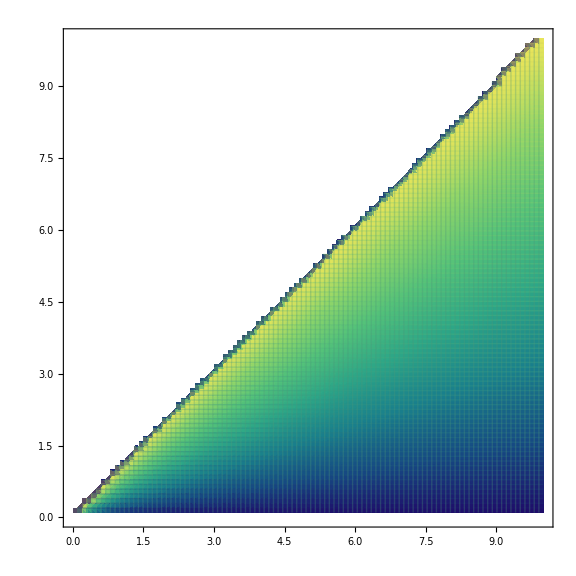

```mathematica
Parasets3=Flatten[Table[{O0[[i]],Ig20[[j]]},{i,Length@O0},{j,Length@Ig20}],1];
data=Flatten[Import[FileNameJoin[{NotebookDirectory[],"list-exp","plot-A="<>ToString@Parasets3[[1]]<>".xlsx"}]],1];
Listplot=Table[{data[[m,1]]-1,data[[m,2]],If[data[[m,4]]<0.0001,-10,100*data[[m,3]]]},{m,Length@data}];
desplot=ListDensityPlot[Listplot,ColorFunction->"BlueGreenYellow",PlotRange->{{0,10},{0,10},{-1,100}},LabelStyle->Directive[Black,Bold,70],Frame->True,FrameStyle->Directive[Thickness[0.006],Black,Bold,70],ImageSize->Large,InterpolationOrder->1.0,Mesh->100]
```